# Least Squares / Linear Regression

Sometimes we’re given some data points of which we need to find a trend line or otherwise known as a regression line.
Let’s say we’re given a couple points, (2, 3) and (7, 4). The points really represent two equations (where we automaticall add a coefficient of 1):
f(2) = β_0+β_1 2 = 3
f(7) = β_0+β_1 7 = 4

(1 | 2
1 | 7)(β_0
β_1) = (3
4)
     A       x⃗         b⃗

If we take the matrix A, augment it with b⃗ and row-reduce the entire thing, you’ll find we get:
(1 | 0 | 13/5
0 | 1 | 1/5)

Now we know our beta parameters:
β_0 = 13/5
β_1 = 1/5

Ok, that’s all cool and all, but sometimes we’ll be given some data where after row-reducing, doesn’t have a solution. The below is an example of a row-reduced matrix.
(1 | 0 | 13/5
0 | 1 | 1/5
0 | 0 | 18/5)

You can see that the bottom row is inconsistent, 0 != 18/5. No line fits these points so we need to find a line that best fits these points, i.e. we need an approximate solution. This leads us to the Least Squares Solution, Ax̂= (b⃗)^∥.

### The Long Way

Let’s first approach this the long way.
Say you have the following points: (2,3),(7,4),(9,8).

Since b⃗is not in the range(A), we need to project it onto the range(A). Therefore, Ax̂= (b⃗)^∥ has a solution even though Ax⃗= b⃗ does not (which commonly happens when m > n). Why (b⃗)^∥? Because it’s the closest vector in range(A) to b⃗ (The Best Approximation Theorem), which means whatever coefficients we get for x⃗is really x̂because they’re approximated.

The algo:
1. Find A.  It’s columns are x[1], x[2] below.  b = {3,4,8}, the “observation” vector.
2. Gram-Schmidt-ify to get an orthogonal basis - v[1],v[2].
3. Find (b⃗)^∥, the orthogonal projection of b⃗ onto span of v[1], v[2]. 
4. Solve Ax̂= (b⃗)^∥.
(1 | 2
1 | 7
1 | 9) * (β_0
β_1) = (3
4
8)

```mathematica
Clear[b,x,proj,v,u]
b={3,4,8};
x[1]={1,1,1};
x[2]={2,7,9};
p=2;(*number of parameters*)
A={x[1],x[2]}ᵀ;
Print["A=",A//MatrixForm]
Print["b=",b//MatrixForm]
```

A=(1 | 2
1 | 7
1 | 9)

b=(3
4
8)

Gram-Schmidt-ify to get an orthogonal basis.

```mathematica
For[i=1,i≤p,i++,
proj[i]=∑_(j=1)^(i-1) ((x[i].v[j])/(v[j].v[j]))v[j];
v[i]=x[i]-proj[i];
u[i]=v[i]/(√(v[i].v[i]));
]
proj[1]=x[1]*0;
T=Table[{x[i]//MatrixForm,proj[i]//Expand//MatrixForm,v[i]//Expand//MatrixForm,u[i]//Expand//MatrixForm},{i,1,p}];
T=Prepend[T,{"original vector","orthogonal projection onto subspace spanned by prior vectors","New Gram-Schmidt-ified vector","Normalized"}];
T=Prepend[T,{"x_i","x_i^∥=∑_(j = 1)^(i - 1) (x_i/v_j)v_j","v_i=x_i-v_i^∥","u_i=v_i/(‖SubscriptBox[v, i]‖)"}];
Print[T//TableForm]
```

x_i | x_i^∥=∑_(j = 1)^(i - 1) (x_i/v_j)v_j | v_i=x_i-v_i^∥ | u_i=v_i/(‖SubscriptBox[v, i]‖)
original vector | orthogonal projection onto subspace spanned by prior vectors | New Gram-Schmidt-ified vector | Normalized
(1
1
1) | (0
0
0) | (1
1
1) | (1/(√3)
1/(√3)
1/(√3))
(2
7
9) | (6
6
6) | (-4
1
3) | (-2 √(2/13)
1/(√26)
3/(√26))

Find (b⃗)^∥.

```mathematica
For[i=1,i≤p,i++,
c[i]=(b.v[i])/(v[i].v[i]);
Print["c[",i,"]=",c[i]]
]
bp=∑_(i=1)^p c[i]*v[i];
Print["b^∥=",bp//MatrixForm]
```

c[1]=5

c[2]=8/13

b^∥=(33/13
73/13
89/13)

Solve Ax̂ = (b⃗)^∥.

```mathematica
B=Append[Aᵀ,bp]ᵀ;
Print["B=[A|b]=",B//MatrixForm];
R=RowReduce[B];
Print["R=rref[B]=",R//MatrixForm];
```

B=[A|b]=(1 | 2 | 33/13
1 | 7 | 73/13
1 | 9 | 89/13)

R=rref[B]=(1 | 0 | 17/13
0 | 1 | 8/13
0 | 0 | 0)

### The Short Way

Now we can use a faster way to solve Ax̂= (b⃗)^∥, using Thm 6.58.13 (the Normal Equation).
Remember that the solutions to Ax̂= (b⃗)^∥are also the solutions to A^T Ax̂ = A^T b⃗.

```mathematica
Aᵀ.A//MatrixForm
Inverse[Aᵀ.A]//MatrixForm
Inverse[Aᵀ.A].Aᵀ//MatrixForm
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual vector = ",e//MatrixForm]
Print["Residual = ",Norm[e]//N]
```

(3 | 18
18 | 134)

(67/39 | -3/13
-3/13 | 1/26)

(49/39 | 4/39 | -14/39
-2/13 | 1/26 | 3/26)

Least squares solution = (17/13
8/13)

Residual vector = (6/13
-21/13
15/13)

Residual = 2.0381

Now a new example with randomly generated data.

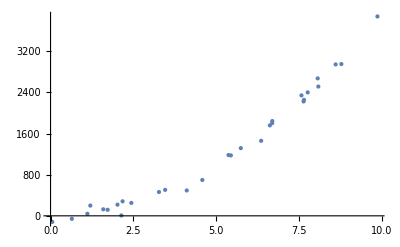

Correlation coefficient is r = 0.970527

Model function is f = {1,t}

A = (1 | 1.1996
1 | 7.7576
1 | 2.13487
1 | 8.05847
1 | 7.63219
1 | 0.0513538
1 | 5.36849
1 | 8.77227
1 | 2.01908
1 | 0.64289
1 | 6.35248
1 | 7.569
1 | 2.43752
1 | 4.10831
1 | 6.615
1 | 1.59084
1 | 2.17268
1 | 1.11084
1 | 6.68779
1 | 5.73913
1 | 8.07761
1 | 3.27042
1 | 3.45693
1 | 7.64491
1 | 4.57847
1 | 8.599
1 | 1.72204
1 | 9.86106
1 | 6.68554
1 | 5.43943)

Least squares solution = (-599.841
379.512)

Residual = 1465.83

Best fit model function = -599.841+379.512 t

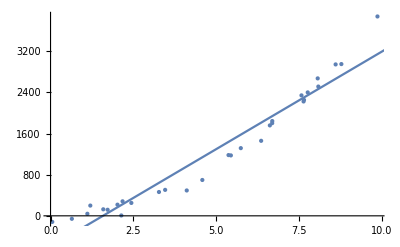

Model function is f = {1,t,t^2}

A = (1 | 1.1996 | 1.43904
1 | 7.7576 | 60.1803
1 | 2.13487 | 4.55769
1 | 8.05847 | 64.9389
1 | 7.63219 | 58.2503
1 | 0.0513538 | 0.00263722
1 | 5.36849 | 28.8207
1 | 8.77227 | 76.9528
1 | 2.01908 | 4.07669
1 | 0.64289 | 0.413308
1 | 6.35248 | 40.354
1 | 7.569 | 57.2897
1 | 2.43752 | 5.94152
1 | 4.10831 | 16.8782
1 | 6.615 | 43.7582
1 | 1.59084 | 2.53076
1 | 2.17268 | 4.72054
1 | 1.11084 | 1.23396
1 | 6.68779 | 44.7266
1 | 5.73913 | 32.9376
1 | 8.07761 | 65.2478
1 | 3.27042 | 10.6956
1 | 3.45693 | 11.9504
1 | 7.64491 | 58.4446
1 | 4.57847 | 20.9624
1 | 8.599 | 73.9428
1 | 1.72204 | 2.96543
1 | 9.86106 | 97.2405
1 | 6.68554 | 44.6965
1 | 5.43943 | 29.5874)

Least squares solution = (-15.4032
1.37295
39.5426)

Residual = 447.123

Best fit model function = -15.4032+1.37295 t+39.5426 t^2

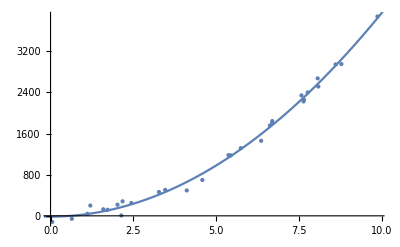

```mathematica
(*generate random data*)
n=30;
M=10;
a=RandomReal[{0,M},n];
g=2-5t+40t^2;
b=g/.{t->a};
e=RandomVariate[NormalDistribution[0,100],n];
b=b+e;
ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]]

(*Compute Correlation coefficient*)
x=a-Mean[a];
y=b-Mean[b];
r=(x.y)/(Norm[x]*Norm[y]);
Print["Correlation coefficient is r = ",N[r]]

(*Establish model*)
Clear[t];
f={1,t};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
Print["A = ",A//MatrixForm];

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]

(*Establish model*)
Clear[t];
f={1,t,t^2};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
Print["A = ",A//MatrixForm];

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]
```

### More Examples

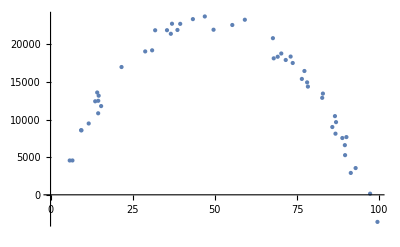

Correlation coefficient is r = -0.254976

Model function is f = {1,t}

Least squares solution = (17094.3
-57.5037)

Residual = 46728.3

Best fit model function = 17094.3-57.5037 t

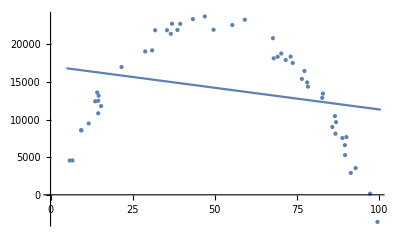

Model function is f = {1,t,t^2}

Least squares solution = (-78.6681
974.294
-10.0404)

Residual = 6682.58

Best fit model function = -78.6681+974.294 t-10.0404 t^2

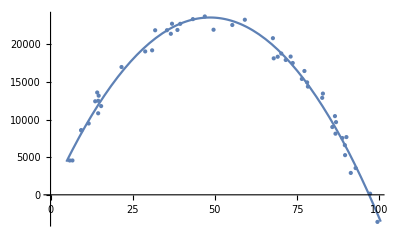

```mathematica
(*generate random data*)
n=50;
M=100;
a=RandomReal[{0,M},n];
g=-9.8t^2+950t;
b=g/.{t->a};
e=RandomVariate[NormalDistribution[0,1000],n];
b=b+e;
ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]]

(*Compute Correlation coefficient*)
x=a-Mean[a];
y=b-Mean[b];
r=(x.y)/(Norm[x]*Norm[y]);
Print["Correlation coefficient is r = ",N[r]]

(*Establish model*)
Clear[t];
f={1,t};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
(*Print["A = ",A//MatrixForm];*)

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]

(*Establish model*)
Clear[t];
f={1,t,t^2};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
(*Print["A = ",A//MatrixForm];*)

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]
```

Yet another example with randomly generated data.

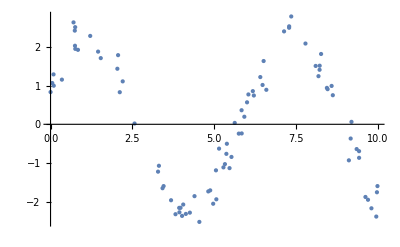

Correlation coefficient is r = -0.216133

Model function is f = {1,t}

Least squares solution = (0.643567
-0.119277)

Residual = 14.4434

Best fit model function = 0.643567-0.119277 t

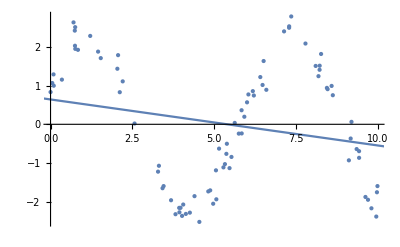

Model function is f = {1,Sin[t],Cos[t]}

Least squares solution = (-0.00117609
2.01716
1.05049)

Residual = 2.74365

Best fit model function = -0.00117609+1.05049 Cos[t]+2.01716 Sin[t]

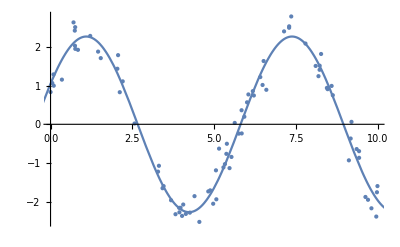

```mathematica
(*generate random data*)
n=85;
M=10;
a=RandomReal[{0,M},n];
g=Cos[t]+2Sin[t];
b=g/.{t->a};
e=RandomVariate[NormalDistribution[0,.3],n];
b=b+e;
ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]]

(*Compute Correlation coefficient*)
x=a-Mean[a];
y=b-Mean[b];
r=(x.y)/(Norm[x]*Norm[y]);
Print["Correlation coefficient is r = ",N[r]]

(*Establish model*)
Clear[t];
f={1,t};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
(*Print["A = ",A//MatrixForm];*)

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]

(*Establish model*)
Clear[t];
f={1,Sin[t],Cos[t]};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
(*Print["A = ",A//MatrixForm];*)

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]
```

Example with non-random data - problem #10 in Section 6.6 (p.376).

Model function is f = {ⅇ^(-0.02 t),ⅇ^(-0.07 t)}

Least squares solution = (19.9411
10.1015)

Residual = 0.0114745

Best fit model function = 10.1015 ⅇ^(-0.07 t)+19.9411 ⅇ^(-0.02 t)

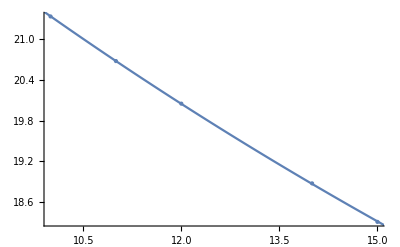

```mathematica
a={10,11,12,14,15};
b={21.34,20.68,20.05,18.87,18.30};

(*Establish model*)
Clear[t];
f={ⅇ^(-0.02t),ⅇ^(-0.07t)};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
(*Print["A = ",A//MatrixForm];*)

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]
```

Example with non-random data - problem #10 in Section 6.6 (p.376).  We get a slightly different answer than the solution manual because their approach has round off error.

Model function is f = {1,Log[t]}

Least squares solution = (17.9243
19.385)

Residual = 0.784091

Best fit model function = 17.9243+19.385 Log[t]

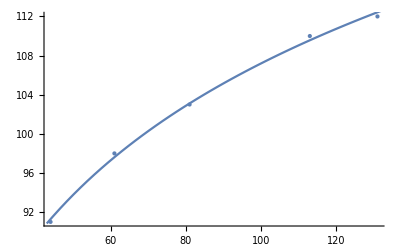

```mathematica
a={44,61,81,113,131};
b={91,98,103,110,112};

(*Establish model*)
Clear[t];
f={1,Log[t]};

(*Construct A*)
A=Table[f/.t->a[[i]],{i,1,Length[a]}];
Print["Model function is f = ",f]
(*Print["A = ",A//MatrixForm];*)

(*Compute and plot least sqaures fit*)
β=Inverse[Aᵀ.A].Aᵀ.b//N;
Print["Least squares solution = ",β//MatrixForm]
e=b-A.β;
Print["Residual = ",Norm[e]//N]
h=f.β;
Print["Best fit model function = ",h]
Show[ListPlot[Transpose[{a,b}],PlotStyle->PointSize[Large]],Plot[h,{t,Min[a]-1,Max[a]+1}]]
```